```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

Fitting model for CA

>> <|chiSquared→1.11232×10^-6,rmsRelativeError→0.380092,rmsRelativeErrorDeaths→0.400336,rmsRelativeErrorPcr→0.363706,meanRelativeErrorDeaths→-0.214996,meanRelativeErrorPcr→0.0341986,rSquaredDeaths→0.0245219,rSquaredPcr→0.0169993,deathResidual7Day→-1.57761,pcrResidual7Day→45.318|>

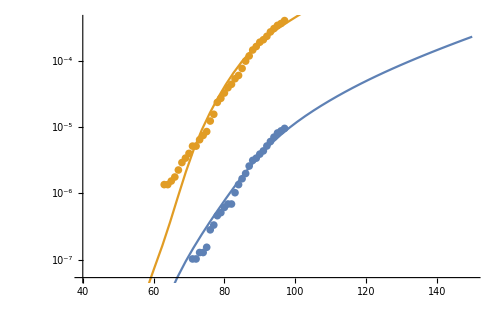
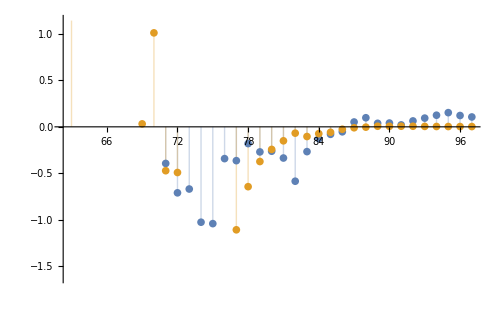
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.80812 | 0.258714 | 14.7194 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[14.7194,58.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 51.6711 | 1.57964 | 32.7107 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[32.7107,58.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 1.6397 | 0.0526521 | 31.1421 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[31.1421,58.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.38529 | 0.270313 | 5.12477 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[5.12477,58.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 7.45548×10^-10 | 1.86387×10^-10
Error | 58 | 1.33596×10^-11 | 2.30337×10^-13
Uncorrected Total | 62 | 7.58907×10^-10 | 
Corrected Total | 61 | 7.43629×10^-10 |

>> Current scenario Generating simulations for CA in the

>> Generating simulations for CA in the  Italy scenario

>> Generating simulations for CA in the  Wuhan scenario

>> Generating simulations for CA in the  Normal scenario

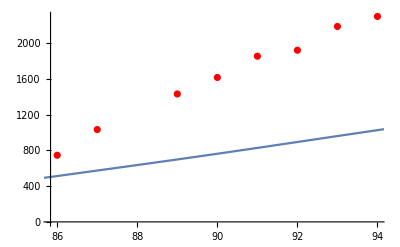
>> -Graphics-

ListPlot::lpn: {{{-854.078,1.}},{}} is not a list of numbers or pairs of numbers.

```mathematica
asd=GenerateModelExport[250,{"CA"}];
```

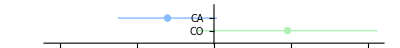

```mathematica
exportAllStatesHospitalizationGoodnessOfFitMetricsSvg["",asd]
```

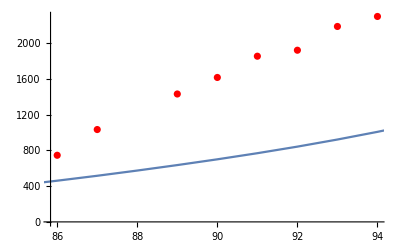

```mathematica
plotStateHospitalization[asd["CA"]]
```